# Math II-Calculus II Project 3

# Using Euler’s Method

## Use Euler’s Method to calculate the first three approximations to the given initial value problem for the specified increment size. Calculate the exact solution and investigate the accuracy of your approximations. 16. y’=ye^x

We make a function to calculate the First Order Differential equation using Euler’s Method

```mathematica
EulersMethod[f_,{y0_,x0_,xn_,h_}]:=Module[{x=x0,y=y0,k1},Reap[While[x<xn,k1=h f[y,x];
y=y+k1;
x=x+h;
Sow[{x,y}];]][[2,1]]]
```

We then make a function in order to pass it through “EulersMethod” function

```mathematica
f[y_,t_]:=y*ⅇ^t
```

We set the value of y(0)=2,  x_0, y_0 and step size n

```mathematica
Solution[n_]:=EulersMethod[f,{2,0,1.5,n}];
```

We then find the exact value to the differential equation using mathematica built-in function called “DSolve”

```mathematica
Df[x_]=DSolve[{y'[x]==y[x]*ⅇ^x,y[0]==2},y[x],x]
```

{{y[x]→2 ⅇ^(-1+ⅇ^x)}}

We then make a function to find the error between the exact value and Euler’s method

```mathematica
error[n_]= Abs[Solution[n]-2 ⅇ^(-1+ⅇ^n)];
```

# Tables of Euler’s Method and Exact Value

```mathematica
TableForm[Solution[0.5],TableHeadings->{None,{"n step size","Euler's Method"}}]//Magnify[#,2]&
```

n step size | Euler's Method
0.5 | 3.
1. | 5.47308
1.5 | 12.9118

```mathematica
TableForm[Table[{n,N[Df[n],20],N[error[n],20]},{n,{0.5,1,1.5}}],TableHeadings->{None,{"n","Exact value","Error"}}]//N //Magnify[#,2]&
```

n | Exact value | Error
0.5 | y[0.5]→3.82619 | 0.826186
1. | y[1.]→11.1499 | 7.14988
1.5 | y[1.5]→65.0292 | 60.0292

## Graphical visualization of the functions

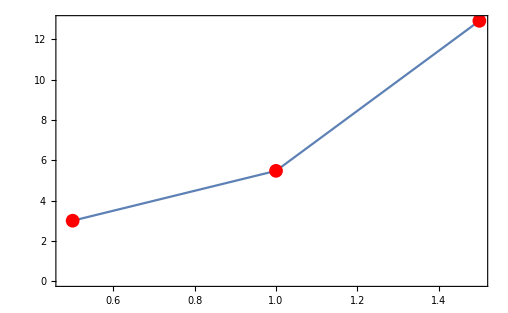

```mathematica
Plot1=ListLinePlot[Solution[0.5],Mesh->All,MeshStyle->Red,PlotRange->All,Frame->True,Epilog->{Red,PointSize[Medium],Point[Solution[0.5]]}]
```

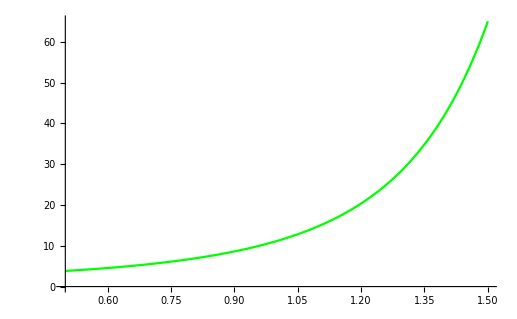

```mathematica
Plot2=Plot[2 ⅇ^(-1+ⅇ^x),{x,0.5,1.5},PlotStyle->Green]
```

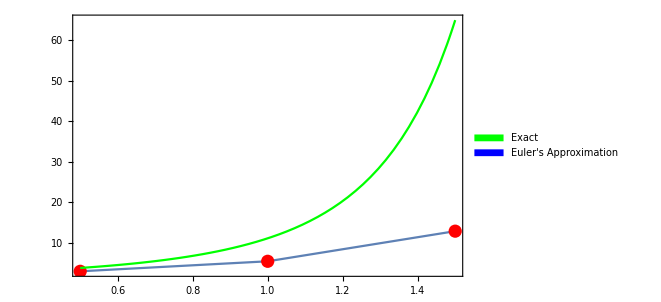

```mathematica
Legended[Show[Plot1,Plot2,PlotRange->All],SwatchLegend[{Green,Blue},{"Exact","Euler's Approximation"}]]
```